The number of pixels and the FFOV are limited by the laser repetition rate, i.e., how many laser pulses fit in a scanned line.
For a 80 MHz laser and 8 kHz scanner, there are 80 MHz/(2*8 kHz) = 5000 pulses. For example, if we have 10 pulses per pixel, then there could be 500 pixels max

```mathematica
μm = 10^-6;
μs=10^-6;
ms=10^-3;
ns = 10^-9;
mm=10^-3;
kHz=10^3;
Tline=63.05μs;(*Time per scanned line*)
Tlaser = 12.5ns;(*Laser pulse repetition period*)
tFPGA = 6.25ns;(*FPGA clock*)
Δx=0.5μm;(*Spatial resolution*)

MaxPulsesPerPixel = 13;
dwell = MaxPulsesPerPixel *Tlaser ;
NpixFFOV=300;(*Effective pixel number. Even number*)
γ = Sin[π/2(NpixFFOV*dwell)/Tline];(*Spatial fill factor*)
FFOV=NpixFFOV * Δx ;(*Full field of view of the microscope)*)
FullScan= FFOV/γ  ;(*Full scan of the RS = distance between turning points*)
```

```mathematica
Grid[{{"Max pulses per pixel",13},{"Pixel dwell time (ns)",dwell/ns},{"Number of pixels",NpixFFOV},{"Fill factor",γ },{"Full scan(μm)",FullScan/μm},{"Full FOV (μm)",FFOV/μm}},Frame->All]
```

Max pulses per pixel | 13
Pixel dwell time (ns) | 162.5
Number of pixels | 300
Fill factor | 0.937207
Full scan(μm) | 160.05
Full FOV (μm) | 150.

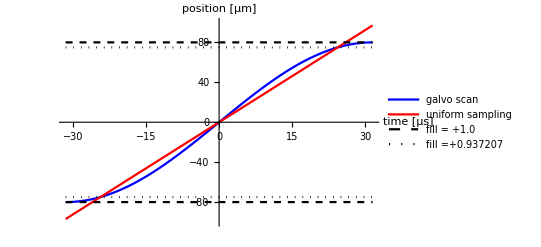

```mathematica
RSposition[t_]:=FullScan/2 Sin[π/Tline t](*Position of the resonant scanner vs time*)
time[x_]:=Tline/π ArcSin[2/FullScan x](*Convert from spatial coordinate to time*)
Plot[{RSposition[t μs]/μm,(FFOV/2)/time[FFOV/2] t μs/μm,{FullScan/2,-FullScan/2}/μm,{-FFOV/2,FFOV/2}/μm },{t,-Tline/2/μs,Tline/2/μs},PlotRange->{-100,100},PlotStyle->{Blue,Red,{Dashed,Black},{Dotted,Black}},AxesLabel->{"time [μs]","position [μm]"} , PlotLegends->{"galvo scan","uniform sampling","fill = +1.0","fill =" +γ}]
```

```mathematica
DiscreteTime[pix_]:=pix * dwell;(*Time discretization*)
DiscretePosition[pix_]:=RSposition[DiscreteTime[pix]](*Spatial discretization mapped from the time discretization*)

(*Tabulate the position vs time*)
NpixFullScan= Round[NpixFFOV/(2γ)]*2;(*Full pixel number. Divide and mulpliy by 2 to get an even number*)
header={"pixel","Time [μs]","Position [μm]"};
TableForm[Prepend[Table[{pix,DiscreteTime[pix]/μs,DiscretePosition[pix]/μm},{pix,NpixFullScan/2,0,-1}],header]]
```

pixel | Time [μs] | Position [μm]
160 | 26. | 77.0117
159 | 25.8375 | 76.8331
158 | 25.675 | 76.6494
157 | 25.5125 | 76.4606
156 | 25.35 | 76.2669
155 | 25.1875 | 76.0682
154 | 25.025 | 75.8645
153 | 24.8625 | 75.6558
152 | 24.7 | 75.4421
151 | 24.5375 | 75.2235
150 | 24.375 | 75.
149 | 24.2125 | 74.7716
148 | 24.05 | 74.5382
147 | 23.8875 | 74.3
146 | 23.725 | 74.0569
145 | 23.5625 | 73.8089
144 | 23.4 | 73.5561
143 | 23.2375 | 73.2985
142 | 23.075 | 73.0361
141 | 22.9125 | 72.7688
140 | 22.75 | 72.4969
139 | 22.5875 | 72.2201
138 | 22.425 | 71.9386
137 | 22.2625 | 71.6525
136 | 22.1 | 71.3616
135 | 21.9375 | 71.066
134 | 21.775 | 70.7658
133 | 21.6125 | 70.4609
132 | 21.45 | 70.1514
131 | 21.2875 | 69.8373
130 | 21.125 | 69.5187
129 | 20.9625 | 69.1955
128 | 20.8 | 68.8677
127 | 20.6375 | 68.5354
126 | 20.475 | 68.1987
125 | 20.3125 | 67.8574
124 | 20.15 | 67.5118
123 | 19.9875 | 67.1617
122 | 19.825 | 66.8071
121 | 19.6625 | 66.4483
120 | 19.5 | 66.085
119 | 19.3375 | 65.7174
118 | 19.175 | 65.3455
117 | 19.0125 | 64.9694
116 | 18.85 | 64.5889
115 | 18.6875 | 64.2043
114 | 18.525 | 63.8154
113 | 18.3625 | 63.4223
112 | 18.2 | 63.0251
111 | 18.0375 | 62.6238
110 | 17.875 | 62.2183
109 | 17.7125 | 61.8088
108 | 17.55 | 61.3952
107 | 17.3875 | 60.9776
106 | 17.225 | 60.556
105 | 17.0625 | 60.1304
104 | 16.9 | 59.7009
103 | 16.7375 | 59.2674
102 | 16.575 | 58.8301
101 | 16.4125 | 58.3889
100 | 16.25 | 57.9439
99 | 16.0875 | 57.4951
98 | 15.925 | 57.0426
97 | 15.7625 | 56.5862
96 | 15.6 | 56.1262
95 | 15.4375 | 55.6625
94 | 15.275 | 55.1952
93 | 15.1125 | 54.7242
92 | 14.95 | 54.2496
91 | 14.7875 | 53.7715
90 | 14.625 | 53.2899
89 | 14.4625 | 52.8048
88 | 14.3 | 52.3162
87 | 14.1375 | 51.8241
86 | 13.975 | 51.3287
85 | 13.8125 | 50.8299
84 | 13.65 | 50.3278
83 | 13.4875 | 49.8224
82 | 13.325 | 49.3137
81 | 13.1625 | 48.8018
80 | 13. | 48.2867
79 | 12.8375 | 47.7684
78 | 12.675 | 47.247
77 | 12.5125 | 46.7225
76 | 12.35 | 46.1949
75 | 12.1875 | 45.6643
74 | 12.025 | 45.1307
73 | 11.8625 | 44.5941
72 | 11.7 | 44.0546
71 | 11.5375 | 43.5123
70 | 11.375 | 42.9671
69 | 11.2125 | 42.419
68 | 11.05 | 41.8682
67 | 10.8875 | 41.3146
66 | 10.725 | 40.7584
65 | 10.5625 | 40.1994
64 | 10.4 | 39.6378
63 | 10.2375 | 39.0737
62 | 10.075 | 38.5069
61 | 9.9125 | 37.9377
60 | 9.75 | 37.3659
59 | 9.5875 | 36.7917
58 | 9.425 | 36.2151
57 | 9.2625 | 35.6361
56 | 9.1 | 35.0548
55 | 8.9375 | 34.4712
54 | 8.775 | 33.8853
53 | 8.6125 | 33.2972
52 | 8.45 | 32.7069
51 | 8.2875 | 32.1145
50 | 8.125 | 31.5199
49 | 7.9625 | 30.9233
48 | 7.8 | 30.3247
47 | 7.6375 | 29.7241
46 | 7.475 | 29.1215
45 | 7.3125 | 28.517
44 | 7.15 | 27.9107
43 | 6.9875 | 27.3025
42 | 6.825 | 26.6925
41 | 6.6625 | 26.0808
40 | 6.5 | 25.4674
39 | 6.3375 | 24.8523
38 | 6.175 | 24.2356
37 | 6.0125 | 23.6173
36 | 5.85 | 22.9974
35 | 5.6875 | 22.376
34 | 5.525 | 21.7532
33 | 5.3625 | 21.1289
32 | 5.2 | 20.5033
31 | 5.0375 | 19.8763
30 | 4.875 | 19.248
29 | 4.7125 | 18.6185
28 | 4.55 | 17.9877
27 | 4.3875 | 17.3557
26 | 4.225 | 16.7226
25 | 4.0625 | 16.0884
24 | 3.9 | 15.4532
23 | 3.7375 | 14.8169
22 | 3.575 | 14.1797
21 | 3.4125 | 13.5416
20 | 3.25 | 12.9025
19 | 3.0875 | 12.2626
18 | 2.925 | 11.6219
17 | 2.7625 | 10.9805
16 | 2.6 | 10.3383
15 | 2.4375 | 9.69543
14 | 2.275 | 9.05194
13 | 2.1125 | 8.40785
12 | 1.95 | 7.76322
11 | 1.7875 | 7.11807
10 | 1.625 | 6.47246
9 | 1.4625 | 5.82642
8 | 1.3 | 5.18001
7 | 1.1375 | 4.53325
6 | 0.975 | 3.88619
5 | 0.8125 | 3.23888
4 | 0.65 | 2.59136
3 | 0.4875 | 1.94367
2 | 0.325 | 1.29585
1 | 0.1625 | 0.647947
0 | 0. | 0.